#### archive

```mathematica
m=500;n=50;
```

```mathematica
δ0=1;Γn=1.;
```

```mathematica
Arand=RandomVariate[NormalDistribution[0,√m*δ0/π],{m,m}];
```

```mathematica
H=I*(Arand-Transpose@Arand);
```

```mathematica
wn=√((m*δ0)/(π^2 Γn)*(2-Γn-2 √(1-Γn)))
```

7.11763

```mathematica
W=DiagonalMatrix[ConstantArray[wn,n],0,{m,n}]
```

{{7.11763,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,7.11763,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},496,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}
 |  |  |  |

```mathematica
W=SparseArray[{Band[{1,1}]->wn},{m,n}];
```

```mathematica
heff=H-I π W. Transpose@W;//AbsoluteTiming
```

{0.0039256,Null}

```mathematica
H
```

$Aborted[]

```mathematica
eig=Eigenvalues[Heff]
```

{-6.23744-0.742913 ⅈ,6.23744-0.742913 ⅈ,-3.87165-0.438649 ⅈ,3.87165-0.438649 ⅈ,-3.25427-0.803059 ⅈ,3.25427-0.803059 ⅈ,-1.36514-0.734197 ⅈ,1.36514-0.734197 ⅈ,-1.46847×10^-15-0.817201 ⅈ,-3.27143×10^-16-0.11136 ⅈ}

```mathematica
{Re[#],Im[#]}&/@eig
```

{{-6.23744,-0.742913},{6.23744,-0.742913},{-3.87165,-0.438649},{3.87165,-0.438649},{-3.25427,-0.803059},{3.25427,-0.803059},{-1.36514,-0.734197},{1.36514,-0.734197},{-1.46847×10^-15,-0.817201},{-3.27143×10^-16,-0.11136}}

#### Code

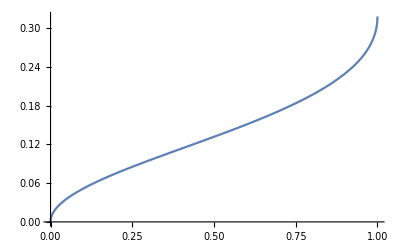

```mathematica
Plot[√((m*δ0)/(π^2 Γn)*(2-Γn-2 √(1-Γn)))/.{Γn->x,m->1,δ0->1},{x,0,1}]
```

```mathematica
HW[m_?IntegerQ,n_?IntegerQ]:=Block[{Arand,H,wn,W,δ0=1.,Γn=1.},Arand=RandomVariate[NormalDistribution[0,√m*δ0/π],{m,m}];H=I*(Arand-Transpose@Arand)/√2;wn=√((m*δ0)/(π^2 Γn)*(2-Γn-2 √(1-Γn)));{H,SparseArray[{Band[{1,1}]->wn},{m,n}]}]
```

```mathematica
Heff[H_,W_]:=H-I π W. Transpose@W
```

```mathematica
S[e_,H_,W_]:=IdentityMatrix[Dimensions[W][[2]]]+2π I Transpose[W].Inverse[(H-I *π *W. Transpose@W-e*IdentityMatrix[Length[H]])].W;
```

```mathematica
G[e_,H_,W_]:=Block[{n=Dimensions[W][[2]],τy,S},S=IdentityMatrix[n]+2π I Transpose[W].Inverse[(H-I *π *W. Transpose@W-e*IdentityMatrix[Length[H]])].W;τy=KroneckerProduct[PauliMatrix[2],IdentityMatrix[n/2]];n/2-1/2*Tr[S.τy.ConjugateTranspose[S].τy]]
```

```mathematica
Gr[e_,H_,W_]:=Block[{n=Dimensions[W][[2]],τy,S,U},S=IdentityMatrix[n]+2π I Transpose[W].Inverse[(H-I *π *W. Transpose@W-e*IdentityMatrix[Length[H]])].W;U=KroneckerProduct[√(1/2){{1,1},{I,-I}},IdentityMatrix[n/2]];S=ConjugateTranspose@U.S.U;n/2-Tr[S[[1;;n/2,1;;n/2]].ConjugateTranspose[S[[1;;n/2,1;;n/2]]]]+Tr[S[[1;;n/2,n/2+1;;n]].ConjugateTranspose[S[[1;;n/2,n/2+1;;n]]]]]
```

```mathematica
PauliMatrix[2]
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
ConjugateTranspose@u.PauliMatrix[3].u
```

{{0,1},{1,0}}

```mathematica
G[1,H1,W1]
```

8.3219×10^-6+0. ⅈ

```mathematica
Gr[1,H1,W1]
```

0.323936+0. ⅈ

```mathematica
S[1,H1,W1][[1,1]]*Conjugate@S[1,H1,W1][[1,1]]+S[1,H1,W1][[1,2]]*Conjugate@S[1,H1,W1][[1,2]]
```

1.+0. ⅈ

```mathematica
S[1,H1,W1][[1;;1,2;;2]]*ConjugateTranspose[S[1,H1,W1][[1;;1,2;;2]]]
```

{{0.00782009+0. ⅈ}}

```mathematica
S[1,H1,W1][[2;;2,2;;2]]*ConjugateTranspose[S[1,H1,W1][[2;;2,2;;2]]]
```

{{0.99218+0. ⅈ}}

```mathematica
S[1,H1,W1][[1;;1,2;;2]]*ConjugateTranspose[S[1,H1,W1][[1;;1,2;;2]]]+S[1,H1,W1][[2;;2,2;;2]]*ConjugateTranspose[S[1,H1,W1][[2;;2,2;;2]]]
```

{{1.+0. ⅈ}}

```mathematica
hwlist=ParallelTable[HW[40,2],100];//AbsoluteTiming
```

{0.0452867,Null}

```mathematica
Hlist=Heff@@@hwlist;//AbsoluteTiming
```

{0.0147139,Null}

```mathematica
eiglist=ParallelTable[Eigenvalues@i,{i,Hlist}];//AbsoluteTiming
```

{0.0967096,Null}

```mathematica
eiglist
```

{{71.5854-0.131915 ⅈ,-71.5854-0.131915 ⅈ,-69.1368-0.0920316 ⅈ,69.1368-0.0920316 ⅈ,-66.1496-0.170708 ⅈ,66.1496-0.170708 ⅈ,-65.101-0.0512918 ⅈ,65.101-0.0512918 ⅈ,62.1924-0.137123 ⅈ,-62.1924-0.137123 ⅈ,61.3503-0.129994 ⅈ,-61.3503-0.129994 ⅈ,59.9346-0.137314 ⅈ,-59.9346-0.137314 ⅈ,-58.9899-0.0710893 ⅈ,58.9899-0.0710893 ⅈ,56.2191-0.119656 ⅈ,-56.2191-0.119656 ⅈ,-54.9008-0.101772 ⅈ,54.9008-0.101772 ⅈ,-54.5885-0.12552 ⅈ,54.5885-0.12552 ⅈ,-53.2796-0.146 ⅈ,53.2796-0.146 ⅈ,52.1192-0.134476 ⅈ,-52.1192-0.134476 ⅈ,-50.8937-0.0765232 ⅈ,50.8937-0.0765232 ⅈ,-49.931-0.0897663 ⅈ,49.931-0.0897663 ⅈ,-47.7357-0.0678632 ⅈ,47.7357-0.0678632 ⅈ,-46.9325-0.187334 ⅈ,46.9325-0.187334 ⅈ,45.272-0.0963296 ⅈ,-45.272-0.0963296 ⅈ,43.7869-0.135344 ⅈ,-43.7869-0.135344 ⅈ,42.2911-0.102941 ⅈ,-42.2911-0.102941 ⅈ,-41.8285-0.0873842 ⅈ,41.8285-0.0873842 ⅈ,40.0414-0.162042 ⅈ,-40.0414-0.162042 ⅈ,39.5418-0.147788 ⅈ,-39.5418-0.147788 ⅈ,37.882-0.0679825 ⅈ,-37.882-0.0679825 ⅈ,36.3564-0.117616 ⅈ,-36.3564-0.117616 ⅈ,35.2968-0.0861887 ⅈ,-35.2968-0.0861887 ⅈ,32.6933-0.0880359 ⅈ,-32.6933-0.0880359 ⅈ,-32.0635-0.0772047 ⅈ,32.0635-0.0772047 ⅈ,31.1721-0.109661 ⅈ,-31.1721-0.109661 ⅈ,-30.1305-0.0486736 ⅈ,30.1305-0.0486736 ⅈ,-28.8595-0.161356 ⅈ,28.8595-0.161356 ⅈ,27.9114-0.142684 ⅈ,-27.9114-0.142684 ⅈ,-27.0062-0.057462 ⅈ,27.0062-0.057462 ⅈ,26.5888-0.0958762 ⅈ,-26.5888-0.0958762 ⅈ,25.8173-0.0965578 ⅈ,-25.8173-0.0965578 ⅈ,23.9822-0.0620401 ⅈ,-23.9822-0.0620401 ⅈ,23.2043-0.0761777 ⅈ,-23.2043-0.0761777 ⅈ,-22.1396-0.0847683 ⅈ,22.1396-0.0847683 ⅈ,21.1127-0.0917108 ⅈ,-21.1127-0.0917108 ⅈ,-19.4157-0.0847078 ⅈ,19.4157-0.0847078 ⅈ,-19.1369-0.097397 ⅈ,19.1369-0.097397 ⅈ,17.6575-0.119624 ⅈ,-17.6575-0.119624 ⅈ,-16.7406-0.111739 ⅈ,16.7406-0.111739 ⅈ,-15.9729-0.113387 ⅈ,15.9729-0.113387 ⅈ,15.0525-0.0874049 ⅈ,-15.0525-0.0874049 ⅈ,-14.1788-0.073417 ⅈ,14.1788-0.073417 ⅈ,-13.2711-0.0522696 ⅈ,13.2711-0.0522696 ⅈ,-11.5297-0.104069 ⅈ,11.5297-0.104069 ⅈ,10.442-0.0824441 ⅈ,-10.442-0.0824441 ⅈ,-9.74572-0.0538256 ⅈ,9.74572-0.0538256 ⅈ,8.76474-0.127713 ⅈ,-8.76474-0.127713 ⅈ,7.86377-0.119417 ⅈ,-7.86377-0.119417 ⅈ,6.86506-0.0340242 ⅈ,-6.86506-0.0340242 ⅈ,6.45716-0.138295 ⅈ,-6.45716-0.138295 ⅈ,5.5114-0.191588 ⅈ,-5.5114-0.191588 ⅈ,4.30958-0.0942979 ⅈ,-4.30958-0.0942979 ⅈ,3.42139-0.144713 ⅈ,-3.42139-0.144713 ⅈ,-2.21907-0.103427 ⅈ,2.21907-0.103427 ⅈ,-0.694101-0.121143 ⅈ,0.694101-0.121143 ⅈ,-0.125531-0.164865 ⅈ,0.125531-0.164865 ⅈ},{-71.1776-0.0856427 ⅈ,71.1776-0.0856427 ⅈ,-70.2897-0.14144 ⅈ,70.2897-0.14144 ⅈ,67.9606-0.0596163 ⅈ,-67.9606-0.0596163 ⅈ,66.1525-0.136114 ⅈ,-66.1525-0.136114 ⅈ,-64.7157-0.181442 ⅈ,64.7157-0.181442 ⅈ,-62.7464-0.0874943 ⅈ,62.7464-0.0874943 ⅈ,-60.5655-0.059006 ⅈ,60.5655-0.059006 ⅈ,58.6982-0.07306 ⅈ,-58.6982-0.07306 ⅈ,-58.1513-0.142303 ⅈ,58.1513-0.142303 ⅈ,56.3206-0.0445095 ⅈ,-56.3206-0.0445095 ⅈ,54.5772-0.121364 ⅈ,-54.5772-0.121364 ⅈ,53.4309-0.122848 ⅈ,-53.4309-0.122848 ⅈ,-51.3802-0.100552 ⅈ,51.3802-0.100552 ⅈ,-50.1217-0.0758448 ⅈ,50.1217-0.0758448 ⅈ,49.1198-0.0760379 ⅈ,-49.1198-0.0760379 ⅈ,-48.3093-0.0804917 ⅈ,48.3093-0.0804917 ⅈ,-46.3971-0.0666109 ⅈ,46.3971-0.0666109 ⅈ,45.0216-0.0670268 ⅈ,-45.0216-0.0670268 ⅈ,-43.5034-0.0472412 ⅈ,43.5034-0.0472412 ⅈ,42.3373-0.116633 ⅈ,-42.3373-0.116633 ⅈ,40.2575-0.0880649 ⅈ,-40.2575-0.0880649 ⅈ,39.5326-0.0684994 ⅈ,-39.5326-0.0684994 ⅈ,38.5394-0.128275 ⅈ,-38.5394-0.128275 ⅈ,-37.5896-0.0686243 ⅈ,37.5896-0.0686243 ⅈ,37.0382-0.132574 ⅈ,-37.0382-0.132574 ⅈ,36.5632-0.119148 ⅈ,-36.5632-0.119148 ⅈ,35.2466-0.238005 ⅈ,-35.2466-0.238005 ⅈ,-33.7893-0.163036 ⅈ,33.7893-0.163036 ⅈ,32.5203-0.158339 ⅈ,-32.5203-0.158339 ⅈ,-31.209-0.128506 ⅈ,31.209-0.128506 ⅈ,-30.514-0.146757 ⅈ,30.514-0.146757 ⅈ,-29.8654-0.0917875 ⅈ,29.8654-0.0917875 ⅈ,28.2523-0.036576 ⅈ,-28.2523-0.036576 ⅈ,27.2431-0.177684 ⅈ,-27.2431-0.177684 ⅈ,-25.8995-0.153761 ⅈ,25.8995-0.153761 ⅈ,-25.8744-0.10938 ⅈ,25.8744-0.10938 ⅈ,-24.5218-0.0554904 ⅈ,24.5218-0.0554904 ⅈ,-23.3366-0.0703515 ⅈ,23.3366-0.0703515 ⅈ,-21.9408-0.101548 ⅈ,21.9408-0.101548 ⅈ,-20.5966-0.0410132 ⅈ,20.5966-0.0410132 ⅈ,-19.7675-0.141934 ⅈ,19.7675-0.141934 ⅈ,19.3754-0.120256 ⅈ,-19.3754-0.120256 ⅈ,-18.0503-0.0521525 ⅈ,18.0503-0.0521525 ⅈ,-16.5314-0.0602332 ⅈ,16.5314-0.0602332 ⅈ,-15.6512-0.0927138 ⅈ,15.6512-0.0927138 ⅈ,14.6637-0.256038 ⅈ,-14.6637-0.256038 ⅈ,-14.0831-0.0697237 ⅈ,14.0831-0.0697237 ⅈ,-12.6941-0.115426 ⅈ,12.6941-0.115426 ⅈ,11.81-0.118777 ⅈ,-11.81-0.118777 ⅈ,-10.9401-0.101685 ⅈ,10.9401-0.101685 ⅈ,9.4727-0.155518 ⅈ,-9.4727-0.155518 ⅈ,-8.37137-0.136418 ⅈ,8.37137-0.136418 ⅈ,7.3917-0.0768202 ⅈ,-7.3917-0.0768202 ⅈ,-6.79561-0.112064 ⅈ,6.79561-0.112064 ⅈ,5.35365-0.0836698 ⅈ,-5.35365-0.0836698 ⅈ,-3.48157-0.0689156 ⅈ,3.48157-0.0689156 ⅈ,3.1475-0.0503596 ⅈ,-3.1475-0.0503596 ⅈ,1.74737-0.139366 ⅈ,-1.74737-0.139366 ⅈ,1.00151-0.123399 ⅈ,-1.00151-0.123399 ⅈ,0.22065-0.147802 ⅈ,-0.22065-0.147802 ⅈ},{75.1107-0.0464951 ⅈ,-75.1107-0.0464951 ⅈ,-70.7284-0.122541 ⅈ,70.7284-0.122541 ⅈ,-67.8116-0.0622479 ⅈ,67.8116-0.0622479 ⅈ,66.4629-0.0530974 ⅈ,-66.4629-0.0530974 ⅈ,65.2445-0.113888 ⅈ,-65.2445-0.113888 ⅈ,-63.5482-0.162952 ⅈ,63.5482-0.162952 ⅈ,61.0224-0.125431 ⅈ,-61.0224-0.125431 ⅈ,-59.4229-0.117782 ⅈ,59.4229-0.117782 ⅈ,57.9878-0.0887598 ⅈ,-57.9878-0.0887598 ⅈ,-56.2066-0.0813714 ⅈ,56.2066-0.0813714 ⅈ,55.1444-0.0555981 ⅈ,-55.1444-0.0555981 ⅈ,54.2498-0.156793 ⅈ,-54.2498-0.156793 ⅈ,51.1032-0.10624 ⅈ,-51.1032-0.10624 ⅈ,49.9073-0.142724 ⅈ,-49.9073-0.142724 ⅈ,49.2249-0.071463 ⅈ,-49.2249-0.071463 ⅈ,-47.6193-0.138343 ⅈ,47.6193-0.138343 ⅈ,45.8547-0.124252 ⅈ,-45.8547-0.124252 ⅈ,-44.5852-0.176983 ⅈ,44.5852-0.176983 ⅈ,43.7197-0.130532 ⅈ,-43.7197-0.130532 ⅈ,-42.3778-0.160639 ⅈ,42.3778-0.160639 ⅈ,41.5996-0.0962011 ⅈ,-41.5996-0.0962011 ⅈ,40.3516-0.108899 ⅈ,-40.3516-0.108899 ⅈ,39.1951-0.0789762 ⅈ,-39.1951-0.0789762 ⅈ,38.9104-0.140491 ⅈ,-38.9104-0.140491 ⅈ,36.9186-0.0915784 ⅈ,-36.9186-0.0915784 ⅈ,-35.6789-0.103718 ⅈ,35.6789-0.103718 ⅈ,-34.3557-0.120576 ⅈ,34.3557-0.120576 ⅈ,-33.5938-0.103139 ⅈ,33.5938-0.103139 ⅈ,32.2188-0.0728303 ⅈ,-32.2188-0.0728303 ⅈ,31.3271-0.0929556 ⅈ,-31.3271-0.0929556 ⅈ,-30.1992-0.122451 ⅈ,30.1992-0.122451 ⅈ,-28.5101-0.119454 ⅈ,28.5101-0.119454 ⅈ,-27.6543-0.112217 ⅈ,27.6543-0.112217 ⅈ,-27.1102-0.0604622 ⅈ,27.1102-0.0604622 ⅈ,25.6362-0.206236 ⅈ,-25.6362-0.206236 ⅈ,25.1473-0.0944504 ⅈ,-25.1473-0.0944504 ⅈ,-23.7039-0.0955522 ⅈ,23.7039-0.0955522 ⅈ,-22.2094-0.127238 ⅈ,22.2094-0.127238 ⅈ,21.5654-0.125467 ⅈ,-21.5654-0.125467 ⅈ,20.5305-0.0694992 ⅈ,-20.5305-0.0694992 ⅈ,20.0011-0.114632 ⅈ,-20.0011-0.114632 ⅈ,-17.9697-0.0581277 ⅈ,17.9697-0.0581277 ⅈ,-17.2908-0.0875888 ⅈ,17.2908-0.0875888 ⅈ,-16.1829-0.150994 ⅈ,16.1829-0.150994 ⅈ,14.8473-0.0978744 ⅈ,-14.8473-0.0978744 ⅈ,14.5876-0.0866143 ⅈ,-14.5876-0.0866143 ⅈ,-12.8814-0.045397 ⅈ,12.8814-0.045397 ⅈ,11.8228-0.145521 ⅈ,-11.8228-0.145521 ⅈ,-10.7192-0.0731338 ⅈ,10.7192-0.0731338 ⅈ,-9.63446-0.113074 ⅈ,9.63446-0.113074 ⅈ,9.3976-0.123107 ⅈ,-9.3976-0.123107 ⅈ,8.31687-0.0592186 ⅈ,-8.31687-0.0592186 ⅈ,7.83546-0.0661158 ⅈ,-7.83546-0.0661158 ⅈ,5.99006-0.082814 ⅈ,-5.99006-0.082814 ⅈ,-5.37876-0.0784052 ⅈ,5.37876-0.0784052 ⅈ,-4.60658-0.0799982 ⅈ,4.60658-0.0799982 ⅈ,3.71604-0.129337 ⅈ,-3.71604-0.129337 ⅈ,3.05144-0.102503 ⅈ,-3.05144-0.102503 ⅈ,1.54657-0.126144 ⅈ,-1.54657-0.126144 ⅈ,0.584183-0.184845 ⅈ,-0.584183-0.184845 ⅈ},{73.7647-0.0844993 ⅈ,-73.7647-0.0844993 ⅈ,-70.3413-0.130315 ⅈ,70.3413-0.130315 ⅈ,-68.5434-0.0777478 ⅈ,68.5434-0.0777478 ⅈ,66.309-0.043552 ⅈ,-66.309-0.043552 ⅈ,-64.1464-0.129392 ⅈ,64.1464-0.129392 ⅈ,62.0918-0.0748816 ⅈ,-62.0918-0.0748816 ⅈ,61.2822-0.174736 ⅈ,-61.2822-0.174736 ⅈ,59.5369-0.0622553 ⅈ,-59.5369-0.0622553 ⅈ,57.6573-0.107119 ⅈ,-57.6573-0.107119 ⅈ,-56.8722-0.222542 ⅈ,56.8722-0.222542 ⅈ,56.0606-0.0665662 ⅈ,-56.0606-0.0665662 ⅈ,-54.027-0.0968695 ⅈ,54.027-0.0968695 ⅈ,52.6307-0.105434 ⅈ,-52.6307-0.105434 ⅈ,51.9292-0.0665889 ⅈ,-51.9292-0.0665889 ⅈ,49.1948-0.111263 ⅈ,-49.1948-0.111263 ⅈ,-47.3836-0.0910891 ⅈ,47.3836-0.0910891 ⅈ,-45.9164-0.073046 ⅈ,45.9164-0.073046 ⅈ,-45.0733-0.174736 ⅈ,45.0733-0.174736 ⅈ,43.9597-0.0513377 ⅈ,-43.9597-0.0513377 ⅈ,-43.3231-0.0860212 ⅈ,43.3231-0.0860212 ⅈ,41.1346-0.127791 ⅈ,-41.1346-0.127791 ⅈ,40.8637-0.0613131 ⅈ,-40.8637-0.0613131 ⅈ,-39.1361-0.065892 ⅈ,39.1361-0.065892 ⅈ,-37.3263-0.0446452 ⅈ,37.3263-0.0446452 ⅈ,36.3545-0.124894 ⅈ,-36.3545-0.124894 ⅈ,-36.0723-0.112409 ⅈ,36.0723-0.112409 ⅈ,34.8899-0.143142 ⅈ,-34.8899-0.143142 ⅈ,-33.7188-0.114221 ⅈ,33.7188-0.114221 ⅈ,-32.1012-0.134811 ⅈ,32.1012-0.134811 ⅈ,-31.5561-0.122764 ⅈ,31.5561-0.122764 ⅈ,30.1892-0.0665416 ⅈ,-30.1892-0.0665416 ⅈ,-29.3444-0.088075 ⅈ,29.3444-0.088075 ⅈ,28.9851-0.0793255 ⅈ,-28.9851-0.0793255 ⅈ,-27.3735-0.0885466 ⅈ,27.3735-0.0885466 ⅈ,-25.7526-0.205879 ⅈ,25.7526-0.205879 ⅈ,24.7079-0.115256 ⅈ,-24.7079-0.115256 ⅈ,23.6662-0.17243 ⅈ,-23.6662-0.17243 ⅈ,-22.5418-0.0629067 ⅈ,22.5418-0.0629067 ⅈ,-21.7204-0.162164 ⅈ,21.7204-0.162164 ⅈ,-20.622-0.057823 ⅈ,20.622-0.057823 ⅈ,19.409-0.176251 ⅈ,-19.409-0.176251 ⅈ,-18.7442-0.136521 ⅈ,18.7442-0.136521 ⅈ,17.7752-0.0902862 ⅈ,-17.7752-0.0902862 ⅈ,16.559-0.105501 ⅈ,-16.559-0.105501 ⅈ,15.8296-0.0859524 ⅈ,-15.8296-0.0859524 ⅈ,14.5463-0.103803 ⅈ,-14.5463-0.103803 ⅈ,-13.6649-0.0732962 ⅈ,13.6649-0.0732962 ⅈ,-12.0657-0.174069 ⅈ,12.0657-0.174069 ⅈ,-11.6775-0.107515 ⅈ,11.6775-0.107515 ⅈ,-10.5633-0.0509988 ⅈ,10.5633-0.0509988 ⅈ,8.93172-0.0596986 ⅈ,-8.93172-0.0596986 ⅈ,-7.5472-0.16285 ⅈ,7.5472-0.16285 ⅈ,6.37392-0.195302 ⅈ,-6.37392-0.195302 ⅈ,-5.79376-0.0628886 ⅈ,5.79376-0.0628886 ⅈ,4.25166-0.148945 ⅈ,-4.25166-0.148945 ⅈ,4.19715-0.0830849 ⅈ,-4.19715-0.0830849 ⅈ,-3.31809-0.0776239 ⅈ,3.31809-0.0776239 ⅈ,2.75637-0.108725 ⅈ,-2.75637-0.108725 ⅈ,1.16464-0.113464 ⅈ,-1.16464-0.113464 ⅈ,-0.396827-0.0883727 ⅈ,0.396827-0.0883727 ⅈ},{74.2711-0.0637608 ⅈ,-74.2711-0.0637608 ⅈ,-70.6158-0.083411 ⅈ,70.6158-0.083411 ⅈ,68.2458-0.155857 ⅈ,-68.2458-0.155857 ⅈ,-65.9335-0.0974062 ⅈ,65.9335-0.0974062 ⅈ,64.0569-0.114765 ⅈ,-64.0569-0.114765 ⅈ,61.7197-0.0896379 ⅈ,-61.7197-0.0896379 ⅈ,-60.2081-0.0688978 ⅈ,60.2081-0.0688978 ⅈ,-59.1069-0.0473014 ⅈ,59.1069-0.0473014 ⅈ,-57.0012-0.0488279 ⅈ,57.0012-0.0488279 ⅈ,-55.8813-0.114063 ⅈ,55.8813-0.114063 ⅈ,-53.7412-0.0407941 ⅈ,53.7412-0.0407941 ⅈ,-52.2169-0.210432 ⅈ,52.2169-0.210432 ⅈ,-51.5032-0.119989 ⅈ,51.5032-0.119989 ⅈ,50.2124-0.0935607 ⅈ,-50.2124-0.0935607 ⅈ,49.3507-0.0476005 ⅈ,-49.3507-0.0476005 ⅈ,47.8575-0.161903 ⅈ,-47.8575-0.161903 ⅈ,47.323-0.124628 ⅈ,-47.323-0.124628 ⅈ,-45.1103-0.123927 ⅈ,45.1103-0.123927 ⅈ,43.9971-0.135653 ⅈ,-43.9971-0.135653 ⅈ,-43.3873-0.11867 ⅈ,43.3873-0.11867 ⅈ,-41.5801-0.102004 ⅈ,41.5801-0.102004 ⅈ,39.9116-0.0917216 ⅈ,-39.9116-0.0917216 ⅈ,38.9709-0.11451 ⅈ,-38.9709-0.11451 ⅈ,37.2753-0.0882409 ⅈ,-37.2753-0.0882409 ⅈ,-36.6493-0.0489078 ⅈ,36.6493-0.0489078 ⅈ,-35.3668-0.178344 ⅈ,35.3668-0.178344 ⅈ,-35.1982-0.0788621 ⅈ,35.1982-0.0788621 ⅈ,-33.4649-0.0853857 ⅈ,33.4649-0.0853857 ⅈ,31.9105-0.161846 ⅈ,-31.9105-0.161846 ⅈ,-30.8424-0.0902307 ⅈ,30.8424-0.0902307 ⅈ,-29.5296-0.099455 ⅈ,29.5296-0.099455 ⅈ,-28.005-0.0909065 ⅈ,28.005-0.0909065 ⅈ,27.3552-0.058095 ⅈ,-27.3552-0.058095 ⅈ,-26.4081-0.095362 ⅈ,26.4081-0.095362 ⅈ,-25.953-0.0996929 ⅈ,25.953-0.0996929 ⅈ,25.27-0.143627 ⅈ,-25.27-0.143627 ⅈ,-23.6457-0.132845 ⅈ,23.6457-0.132845 ⅈ,-22.4475-0.117202 ⅈ,22.4475-0.117202 ⅈ,20.9017-0.131266 ⅈ,-20.9017-0.131266 ⅈ,20.5645-0.172569 ⅈ,-20.5645-0.172569 ⅈ,19.3189-0.137917 ⅈ,-19.3189-0.137917 ⅈ,-18.458-0.134452 ⅈ,18.458-0.134452 ⅈ,18.1483-0.119066 ⅈ,-18.1483-0.119066 ⅈ,-17.0535-0.0929986 ⅈ,17.0535-0.0929986 ⅈ,-15.7485-0.12441 ⅈ,15.7485-0.12441 ⅈ,14.2204-0.127454 ⅈ,-14.2204-0.127454 ⅈ,-13.0192-0.0748973 ⅈ,13.0192-0.0748973 ⅈ,-12.0503-0.0657146 ⅈ,12.0503-0.0657146 ⅈ,-11.4591-0.0683315 ⅈ,11.4591-0.0683315 ⅈ,-10.2782-0.0806472 ⅈ,10.2782-0.0806472 ⅈ,-9.53685-0.0700643 ⅈ,9.53685-0.0700643 ⅈ,-8.07516-0.131332 ⅈ,8.07516-0.131332 ⅈ,6.47279-0.0715237 ⅈ,-6.47279-0.0715237 ⅈ,-5.61363-0.109683 ⅈ,5.61363-0.109683 ⅈ,-4.98702-0.0982219 ⅈ,4.98702-0.0982219 ⅈ,4.12371-0.209266 ⅈ,-4.12371-0.209266 ⅈ,3.18549-0.096356 ⅈ,-3.18549-0.096356 ⅈ,-2.32784-0.03436 ⅈ,2.32784-0.03436 ⅈ,1.01428-0.108814 ⅈ,-1.01428-0.108814 ⅈ,-3.65973×10^-15-0.295946 ⅈ,-1.05702×10^-15-0.0806552 ⅈ},{-72.5869-0.0761634 ⅈ,72.5869-0.0761634 ⅈ,68.3175-0.116545 ⅈ,-68.3175-0.116545 ⅈ,67.0062-0.0900671 ⅈ,-67.0062-0.0900671 ⅈ,66.6355-0.10564 ⅈ,-66.6355-0.10564 ⅈ,-62.715-0.0531046 ⅈ,62.715-0.0531046 ⅈ,60.5792-0.148247 ⅈ,-60.5792-0.148247 ⅈ,-59.6599-0.069644 ⅈ,59.6599-0.069644 ⅈ,58.0434-0.122107 ⅈ,-58.0434-0.122107 ⅈ,56.36-0.133433 ⅈ,-56.36-0.133433 ⅈ,55.3648-0.0626372 ⅈ,-55.3648-0.0626372 ⅈ,-53.9512-0.0281047 ⅈ,53.9512-0.0281047 ⅈ,52.0836-0.0822787 ⅈ,-52.0836-0.0822787 ⅈ,50.6731-0.0852001 ⅈ,-50.6731-0.0852001 ⅈ,-49.7142-0.0726811 ⅈ,49.7142-0.0726811 ⅈ,-48.5502-0.0768094 ⅈ,48.5502-0.0768094 ⅈ,-46.31-0.0756104 ⅈ,46.31-0.0756104 ⅈ,-46.1065-0.0967609 ⅈ,46.1065-0.0967609 ⅈ,44.7606-0.0748527 ⅈ,-44.7606-0.0748527 ⅈ,-43.5932-0.103593 ⅈ,43.5932-0.103593 ⅈ,43.0156-0.0880302 ⅈ,-43.0156-0.0880302 ⅈ,41.3946-0.0801268 ⅈ,-41.3946-0.0801268 ⅈ,-40.6435-0.113176 ⅈ,40.6435-0.113176 ⅈ,-38.9958-0.131811 ⅈ,38.9958-0.131811 ⅈ,-36.9599-0.0746662 ⅈ,36.9599-0.0746662 ⅈ,36.5309-0.127642 ⅈ,-36.5309-0.127642 ⅈ,35.3598-0.166983 ⅈ,-35.3598-0.166983 ⅈ,34.9252-0.0838293 ⅈ,-34.9252-0.0838293 ⅈ,-33.7125-0.167743 ⅈ,33.7125-0.167743 ⅈ,32.6233-0.0764066 ⅈ,-32.6233-0.0764066 ⅈ,-32.356-0.130609 ⅈ,32.356-0.130609 ⅈ,-29.9297-0.0604264 ⅈ,29.9297-0.0604264 ⅈ,-28.8712-0.100761 ⅈ,28.8712-0.100761 ⅈ,-28.0535-0.0923513 ⅈ,28.0535-0.0923513 ⅈ,-27.0247-0.110275 ⅈ,27.0247-0.110275 ⅈ,-26.4539-0.0613486 ⅈ,26.4539-0.0613486 ⅈ,25.1035-0.264112 ⅈ,-25.1035-0.264112 ⅈ,23.9587-0.13039 ⅈ,-23.9587-0.13039 ⅈ,-23.4022-0.114885 ⅈ,23.4022-0.114885 ⅈ,-22.4-0.0806981 ⅈ,22.4-0.0806981 ⅈ,-22.0146-0.159235 ⅈ,22.0146-0.159235 ⅈ,20.4212-0.0760755 ⅈ,-20.4212-0.0760755 ⅈ,18.7846-0.0936979 ⅈ,-18.7846-0.0936979 ⅈ,18.5219-0.132037 ⅈ,-18.5219-0.132037 ⅈ,16.5174-0.118255 ⅈ,-16.5174-0.118255 ⅈ,15.7476-0.160177 ⅈ,-15.7476-0.160177 ⅈ,14.7397-0.115154 ⅈ,-14.7397-0.115154 ⅈ,14.1589-0.0566158 ⅈ,-14.1589-0.0566158 ⅈ,12.6724-0.143863 ⅈ,-12.6724-0.143863 ⅈ,11.4028-0.196841 ⅈ,-11.4028-0.196841 ⅈ,10.3547-0.149531 ⅈ,-10.3547-0.149531 ⅈ,9.15445-0.0662355 ⅈ,-9.15445-0.0662355 ⅈ,7.42248-0.138548 ⅈ,-7.42248-0.138548 ⅈ,6.83412-0.0935294 ⅈ,-6.83412-0.0935294 ⅈ,-5.66479-0.0817048 ⅈ,5.66479-0.0817048 ⅈ,-5.34572-0.0983874 ⅈ,5.34572-0.0983874 ⅈ,4.03921-0.0682075 ⅈ,-4.03921-0.0682075 ⅈ,3.42316-0.131515 ⅈ,-3.42316-0.131515 ⅈ,-2.06623-0.0960007 ⅈ,2.06623-0.0960007 ⅈ,1.50061-0.107377 ⅈ,-1.50061-0.107377 ⅈ,-0.654207-0.17323 ⅈ,0.654207-0.17323 ⅈ},{-72.8903-0.108847 ⅈ,72.8903-0.108847 ⅈ,-71.2599-0.0322032 ⅈ,71.2599-0.0322032 ⅈ,69.9941-0.109717 ⅈ,-69.9941-0.109717 ⅈ,-65.209-0.124805 ⅈ,65.209-0.124805 ⅈ,-63.9574-0.0604772 ⅈ,63.9574-0.0604772 ⅈ,62.9044-0.154667 ⅈ,-62.9044-0.154667 ⅈ,59.8286-0.0741726 ⅈ,-59.8286-0.0741726 ⅈ,-57.6436-0.0859769 ⅈ,57.6436-0.0859769 ⅈ,57.3908-0.081111 ⅈ,-57.3908-0.081111 ⅈ,-56.0394-0.127161 ⅈ,56.0394-0.127161 ⅈ,54.1505-0.125013 ⅈ,-54.1505-0.125013 ⅈ,-53.5819-0.0841589 ⅈ,53.5819-0.0841589 ⅈ,-52.9259-0.120737 ⅈ,52.9259-0.120737 ⅈ,50.6046-0.0470491 ⅈ,-50.6046-0.0470491 ⅈ,-49.983-0.112332 ⅈ,49.983-0.112332 ⅈ,-47.452-0.0597841 ⅈ,47.452-0.0597841 ⅈ,46.3934-0.100566 ⅈ,-46.3934-0.100566 ⅈ,-45.0949-0.053783 ⅈ,45.0949-0.053783 ⅈ,-43.915-0.105929 ⅈ,43.915-0.105929 ⅈ,42.4389-0.08106 ⅈ,-42.4389-0.08106 ⅈ,41.432-0.0434743 ⅈ,-41.432-0.0434743 ⅈ,40.5377-0.105095 ⅈ,-40.5377-0.105095 ⅈ,-39.5976-0.146869 ⅈ,39.5976-0.146869 ⅈ,-37.8117-0.27332 ⅈ,37.8117-0.27332 ⅈ,35.9719-0.133422 ⅈ,-35.9719-0.133422 ⅈ,35.4398-0.095634 ⅈ,-35.4398-0.095634 ⅈ,-34.8033-0.135836 ⅈ,34.8033-0.135836 ⅈ,-32.8843-0.103455 ⅈ,32.8843-0.103455 ⅈ,32.6157-0.115556 ⅈ,-32.6157-0.115556 ⅈ,31.5693-0.0867462 ⅈ,-31.5693-0.0867462 ⅈ,-30.4159-0.160793 ⅈ,30.4159-0.160793 ⅈ,28.6664-0.122104 ⅈ,-28.6664-0.122104 ⅈ,-27.3295-0.130553 ⅈ,27.3295-0.130553 ⅈ,-26.2298-0.0963309 ⅈ,26.2298-0.0963309 ⅈ,-25.7535-0.141826 ⅈ,25.7535-0.141826 ⅈ,24.3399-0.140685 ⅈ,-24.3399-0.140685 ⅈ,-23.0995-0.0503328 ⅈ,23.0995-0.0503328 ⅈ,-21.695-0.0643483 ⅈ,21.695-0.0643483 ⅈ,21.0344-0.121388 ⅈ,-21.0344-0.121388 ⅈ,-19.4746-0.10662 ⅈ,19.4746-0.10662 ⅈ,19.0676-0.161186 ⅈ,-19.0676-0.161186 ⅈ,18.4048-0.0794458 ⅈ,-18.4048-0.0794458 ⅈ,-17.4062-0.069781 ⅈ,17.4062-0.069781 ⅈ,16.4611-0.052367 ⅈ,-16.4611-0.052367 ⅈ,-14.8186-0.126429 ⅈ,14.8186-0.126429 ⅈ,13.9727-0.0946126 ⅈ,-13.9727-0.0946126 ⅈ,13.0668-0.126398 ⅈ,-13.0668-0.126398 ⅈ,12.6024-0.100956 ⅈ,-12.6024-0.100956 ⅈ,-11.2251-0.127325 ⅈ,11.2251-0.127325 ⅈ,10.6423-0.143809 ⅈ,-10.6423-0.143809 ⅈ,-8.98534-0.0433417 ⅈ,8.98534-0.0433417 ⅈ,-7.95214-0.159729 ⅈ,7.95214-0.159729 ⅈ,-7.32977-0.12592 ⅈ,7.32977-0.12592 ⅈ,6.8155-0.118497 ⅈ,-6.8155-0.118497 ⅈ,-5.74608-0.0882966 ⅈ,5.74608-0.0882966 ⅈ,-4.21975-0.0570529 ⅈ,4.21975-0.0570529 ⅈ,-3.17637-0.088825 ⅈ,3.17637-0.088825 ⅈ,-2.03092-0.134254 ⅈ,2.03092-0.134254 ⅈ,-1.18521-0.069809 ⅈ,1.18521-0.069809 ⅈ,-0.185752-0.193996 ⅈ,0.185752-0.193996 ⅈ},{-73.8056-0.120091 ⅈ,73.8056-0.120091 ⅈ,-72.59-0.124044 ⅈ,72.59-0.124044 ⅈ,70.0493-0.136961 ⅈ,-70.0493-0.136961 ⅈ,-65.6849-0.113106 ⅈ,65.6849-0.113106 ⅈ,-63.088-0.111865 ⅈ,63.088-0.111865 ⅈ,-62.2538-0.171733 ⅈ,62.2538-0.171733 ⅈ,-60.9754-0.106773 ⅈ,60.9754-0.106773 ⅈ,-58.8913-0.12346 ⅈ,58.8913-0.12346 ⅈ,-57.1274-0.0866993 ⅈ,57.1274-0.0866993 ⅈ,56.1263-0.0619388 ⅈ,-56.1263-0.0619388 ⅈ,-55.3933-0.0992854 ⅈ,55.3933-0.0992854 ⅈ,-53.6721-0.154556 ⅈ,53.6721-0.154556 ⅈ,-51.7213-0.0779387 ⅈ,51.7213-0.0779387 ⅈ,50.2071-0.0805731 ⅈ,-50.2071-0.0805731 ⅈ,49.0836-0.190309 ⅈ,-49.0836-0.190309 ⅈ,47.8013-0.0951728 ⅈ,-47.8013-0.0951728 ⅈ,47.1157-0.0657062 ⅈ,-47.1157-0.0657062 ⅈ,46.2428-0.0999536 ⅈ,-46.2428-0.0999536 ⅈ,44.1225-0.0665015 ⅈ,-44.1225-0.0665015 ⅈ,-43.4321-0.0777708 ⅈ,43.4321-0.0777708 ⅈ,-42.0376-0.180506 ⅈ,42.0376-0.180506 ⅈ,41.0667-0.119397 ⅈ,-41.0667-0.119397 ⅈ,-39.4266-0.107139 ⅈ,39.4266-0.107139 ⅈ,-38.6656-0.116002 ⅈ,38.6656-0.116002 ⅈ,37.3892-0.0822279 ⅈ,-37.3892-0.0822279 ⅈ,-35.9881-0.0712698 ⅈ,35.9881-0.0712698 ⅈ,-34.6273-0.114813 ⅈ,34.6273-0.114813 ⅈ,-33.8678-0.0557891 ⅈ,33.8678-0.0557891 ⅈ,-32.8712-0.0487317 ⅈ,32.8712-0.0487317 ⅈ,-32.1454-0.113806 ⅈ,32.1454-0.113806 ⅈ,-31.1546-0.0615951 ⅈ,31.1546-0.0615951 ⅈ,-29.7902-0.208588 ⅈ,29.7902-0.208588 ⅈ,27.9534-0.0561287 ⅈ,-27.9534-0.0561287 ⅈ,-27.1138-0.036702 ⅈ,27.1138-0.036702 ⅈ,-26.1001-0.0974967 ⅈ,26.1001-0.0974967 ⅈ,-25.4099-0.116895 ⅈ,25.4099-0.116895 ⅈ,-24.4412-0.112325 ⅈ,24.4412-0.112325 ⅈ,22.7576-0.127143 ⅈ,-22.7576-0.127143 ⅈ,22.3429-0.112422 ⅈ,-22.3429-0.112422 ⅈ,-21.701-0.142454 ⅈ,21.701-0.142454 ⅈ,-20.5629-0.146546 ⅈ,20.5629-0.146546 ⅈ,19.0082-0.111593 ⅈ,-19.0082-0.111593 ⅈ,18.0451-0.080204 ⅈ,-18.0451-0.080204 ⅈ,-17.7161-0.0876762 ⅈ,17.7161-0.0876762 ⅈ,-16.4157-0.058688 ⅈ,16.4157-0.058688 ⅈ,14.5244-0.202513 ⅈ,-14.5244-0.202513 ⅈ,-13.8262-0.0695963 ⅈ,13.8262-0.0695963 ⅈ,-13.2594-0.0844212 ⅈ,13.2594-0.0844212 ⅈ,12.2225-0.0982246 ⅈ,-12.2225-0.0982246 ⅈ,-12.0154-0.104979 ⅈ,12.0154-0.104979 ⅈ,10.3218-0.0338755 ⅈ,-10.3218-0.0338755 ⅈ,8.6577-0.108011 ⅈ,-8.6577-0.108011 ⅈ,7.87485-0.0833683 ⅈ,-7.87485-0.0833683 ⅈ,6.28569-0.146474 ⅈ,-6.28569-0.146474 ⅈ,-5.81764-0.0977643 ⅈ,5.81764-0.0977643 ⅈ,-4.67714-0.0957207 ⅈ,4.67714-0.0957207 ⅈ,-4.34002-0.112072 ⅈ,4.34002-0.112072 ⅈ,-2.3422-0.160972 ⅈ,2.3422-0.160972 ⅈ,-1.42114-0.106945 ⅈ,1.42114-0.106945 ⅈ,-0.510596-0.150457 ⅈ,0.510596-0.150457 ⅈ},{-73.8691-0.119708 ⅈ,73.8691-0.119708 ⅈ,71.1883-0.0601505 ⅈ,-71.1883-0.0601505 ⅈ,-68.8162-0.116258 ⅈ,68.8162-0.116258 ⅈ,67.4566-0.0836485 ⅈ,-67.4566-0.0836485 ⅈ,64.843-0.214537 ⅈ,-64.843-0.214537 ⅈ,63.8907-0.118539 ⅈ,-63.8907-0.118539 ⅈ,62.3613-0.0894352 ⅈ,-62.3613-0.0894352 ⅈ,-60.1737-0.085668 ⅈ,60.1737-0.085668 ⅈ,58.5462-0.06365 ⅈ,-58.5462-0.06365 ⅈ,56.4285-0.11876 ⅈ,-56.4285-0.11876 ⅈ,-56.016-0.0829381 ⅈ,56.016-0.0829381 ⅈ,54.2044-0.194934 ⅈ,-54.2044-0.194934 ⅈ,-51.9844-0.146083 ⅈ,51.9844-0.146083 ⅈ,50.7598-0.220869 ⅈ,-50.7598-0.220869 ⅈ,49.1996-0.0404248 ⅈ,-49.1996-0.0404248 ⅈ,48.8062-0.0713241 ⅈ,-48.8062-0.0713241 ⅈ,47.2688-0.0831448 ⅈ,-47.2688-0.0831448 ⅈ,45.4114-0.173947 ⅈ,-45.4114-0.173947 ⅈ,44.2651-0.0543355 ⅈ,-44.2651-0.0543355 ⅈ,43.2272-0.139468 ⅈ,-43.2272-0.139468 ⅈ,-42.4067-0.073903 ⅈ,42.4067-0.073903 ⅈ,-40.7978-0.0943107 ⅈ,40.7978-0.0943107 ⅈ,39.9896-0.183125 ⅈ,-39.9896-0.183125 ⅈ,38.7074-0.0700492 ⅈ,-38.7074-0.0700492 ⅈ,37.7214-0.0773875 ⅈ,-37.7214-0.0773875 ⅈ,37.0127-0.138825 ⅈ,-37.0127-0.138825 ⅈ,-35.1667-0.0453712 ⅈ,35.1667-0.0453712 ⅈ,-33.4038-0.0823142 ⅈ,33.4038-0.0823142 ⅈ,32.8238-0.10608 ⅈ,-32.8238-0.10608 ⅈ,-30.2378-0.138397 ⅈ,30.2378-0.138397 ⅈ,29.6201-0.0891573 ⅈ,-29.6201-0.0891573 ⅈ,-28.5276-0.0571823 ⅈ,28.5276-0.0571823 ⅈ,-27.7224-0.0932617 ⅈ,27.7224-0.0932617 ⅈ,-26.6288-0.0658253 ⅈ,26.6288-0.0658253 ⅈ,-25.7692-0.123765 ⅈ,25.7692-0.123765 ⅈ,25.0141-0.12138 ⅈ,-25.0141-0.12138 ⅈ,23.9112-0.088087 ⅈ,-23.9112-0.088087 ⅈ,-22.7013-0.0733876 ⅈ,22.7013-0.0733876 ⅈ,21.7626-0.0703697 ⅈ,-21.7626-0.0703697 ⅈ,20.1981-0.0589238 ⅈ,-20.1981-0.0589238 ⅈ,18.7584-0.203938 ⅈ,-18.7584-0.203938 ⅈ,-18.6185-0.0790702 ⅈ,18.6185-0.0790702 ⅈ,-17.1133-0.148597 ⅈ,17.1133-0.148597 ⅈ,-16.2655-0.0392215 ⅈ,16.2655-0.0392215 ⅈ,15.8245-0.141826 ⅈ,-15.8245-0.141826 ⅈ,13.7733-0.0627465 ⅈ,-13.7733-0.0627465 ⅈ,12.4908-0.0374748 ⅈ,-12.4908-0.0374748 ⅈ,12.103-0.145904 ⅈ,-12.103-0.145904 ⅈ,11.6766-0.102594 ⅈ,-11.6766-0.102594 ⅈ,-10.3957-0.117336 ⅈ,10.3957-0.117336 ⅈ,-8.77997-0.108567 ⅈ,8.77997-0.108567 ⅈ,-7.54169-0.103059 ⅈ,7.54169-0.103059 ⅈ,-7.29543-0.188305 ⅈ,7.29543-0.188305 ⅈ,6.51675-0.078243 ⅈ,-6.51675-0.078243 ⅈ,-5.92468-0.0651776 ⅈ,5.92468-0.0651776 ⅈ,4.43403-0.173905 ⅈ,-4.43403-0.173905 ⅈ,3.53415-0.101715 ⅈ,-3.53415-0.101715 ⅈ,1.93544-0.177464 ⅈ,-1.93544-0.177464 ⅈ,-1.29846-0.0553243 ⅈ,1.29846-0.0553243 ⅈ,-2.88299×10^-15-0.180457 ⅈ,-1.60595×10^-15-0.0726918 ⅈ},{73.5788-0.112492 ⅈ,-73.5788-0.112492 ⅈ,-69.234-0.180763 ⅈ,69.234-0.180763 ⅈ,68.2804-0.0994722 ⅈ,-68.2804-0.0994722 ⅈ,65.8149-0.0905878 ⅈ,-65.8149-0.0905878 ⅈ,-64.0074-0.0445083 ⅈ,64.0074-0.0445083 ⅈ,-62.399-0.105693 ⅈ,62.399-0.105693 ⅈ,61.1543-0.173015 ⅈ,-61.1543-0.173015 ⅈ,60.0258-0.117325 ⅈ,-60.0258-0.117325 ⅈ,-57.0735-0.100975 ⅈ,57.0735-0.100975 ⅈ,56.2561-0.0819446 ⅈ,-56.2561-0.0819446 ⅈ,-54.9739-0.110061 ⅈ,54.9739-0.110061 ⅈ,-52.0887-0.152495 ⅈ,52.0887-0.152495 ⅈ,50.8901-0.084618 ⅈ,-50.8901-0.084618 ⅈ,50.4379-0.137178 ⅈ,-50.4379-0.137178 ⅈ,49.374-0.109547 ⅈ,-49.374-0.109547 ⅈ,-48.7578-0.104763 ⅈ,48.7578-0.104763 ⅈ,47.041-0.114918 ⅈ,-47.041-0.114918 ⅈ,-46.0746-0.192611 ⅈ,46.0746-0.192611 ⅈ,-44.4908-0.106561 ⅈ,44.4908-0.106561 ⅈ,-42.7055-0.0583699 ⅈ,42.7055-0.0583699 ⅈ,41.1735-0.100449 ⅈ,-41.1735-0.100449 ⅈ,39.6465-0.0755913 ⅈ,-39.6465-0.0755913 ⅈ,38.7646-0.047205 ⅈ,-38.7646-0.047205 ⅈ,-37.6464-0.0911236 ⅈ,37.6464-0.0911236 ⅈ,-36.9684-0.139155 ⅈ,36.9684-0.139155 ⅈ,36.001-0.100527 ⅈ,-36.001-0.100527 ⅈ,35.3085-0.102722 ⅈ,-35.3085-0.102722 ⅈ,-34.1762-0.0609885 ⅈ,34.1762-0.0609885 ⅈ,32.7472-0.139537 ⅈ,-32.7472-0.139537 ⅈ,31.6462-0.0649467 ⅈ,-31.6462-0.0649467 ⅈ,-30.3678-0.0724248 ⅈ,30.3678-0.0724248 ⅈ,-29.3768-0.0843221 ⅈ,29.3768-0.0843221 ⅈ,-28.3253-0.114833 ⅈ,28.3253-0.114833 ⅈ,-27.4656-0.137791 ⅈ,27.4656-0.137791 ⅈ,26.1353-0.052533 ⅈ,-26.1353-0.052533 ⅈ,-24.2526-0.158135 ⅈ,24.2526-0.158135 ⅈ,22.9246-0.0822524 ⅈ,-22.9246-0.0822524 ⅈ,21.9146-0.140561 ⅈ,-21.9146-0.140561 ⅈ,-21.5735-0.0422342 ⅈ,21.5735-0.0422342 ⅈ,20.9298-0.115754 ⅈ,-20.9298-0.115754 ⅈ,20.3717-0.0353011 ⅈ,-20.3717-0.0353011 ⅈ,-18.3721-0.0895714 ⅈ,18.3721-0.0895714 ⅈ,17.9316-0.084187 ⅈ,-17.9316-0.084187 ⅈ,-16.675-0.0674635 ⅈ,16.675-0.0674635 ⅈ,15.2419-0.0954444 ⅈ,-15.2419-0.0954444 ⅈ,14.6189-0.18768 ⅈ,-14.6189-0.18768 ⅈ,-13.7438-0.0598908 ⅈ,13.7438-0.0598908 ⅈ,-13.454-0.064395 ⅈ,13.454-0.064395 ⅈ,-12.1474-0.0893996 ⅈ,12.1474-0.0893996 ⅈ,-10.6592-0.143699 ⅈ,10.6592-0.143699 ⅈ,9.96816-0.0872868 ⅈ,-9.96816-0.0872868 ⅈ,8.53189-0.177468 ⅈ,-8.53189-0.177468 ⅈ,7.79-0.0770623 ⅈ,-7.79-0.0770623 ⅈ,-6.90656-0.215898 ⅈ,6.90656-0.215898 ⅈ,-6.00787-0.0640953 ⅈ,6.00787-0.0640953 ⅈ,-4.66249-0.147447 ⅈ,4.66249-0.147447 ⅈ,-2.91453-0.178364 ⅈ,2.91453-0.178364 ⅈ,2.16122-0.085342 ⅈ,-2.16122-0.085342 ⅈ,1.82093-0.123055 ⅈ,-1.82093-0.123055 ⅈ,-5.85716×10^-16-0.162808 ⅈ,1.65555×10^-15-0.0610611 ⅈ}}

#### Γn=1

```mathematica
Graphics[Point[{Re[#],Im[#]}&/@Flatten@eiglist],Axes->True,AspectRatio->1,AxesOrigin->{0,0},PlotRange->{{-1,1},{-100,0}}]
```

-Graphics-

#### Γn=0.2

```mathematica
Graphics[Point[{Re[#],Im[#]}&/@Flatten@eiglist],Axes->True,AspectRatio->1,AxesOrigin->{0,0},PlotRange->{{-1,1},Automatic}]
```

-Graphics-

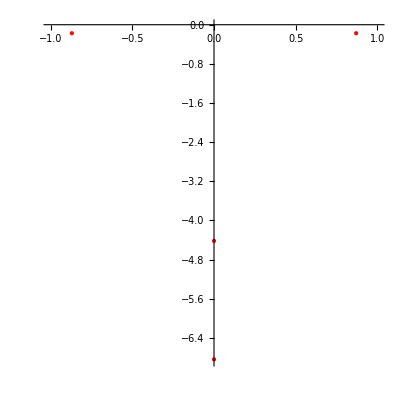
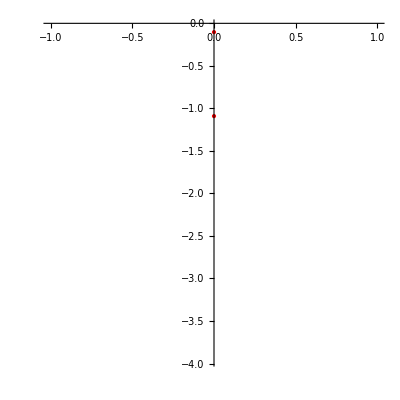
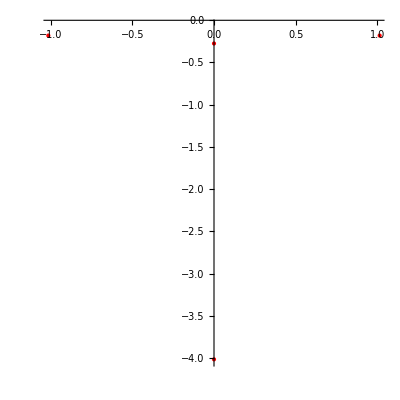
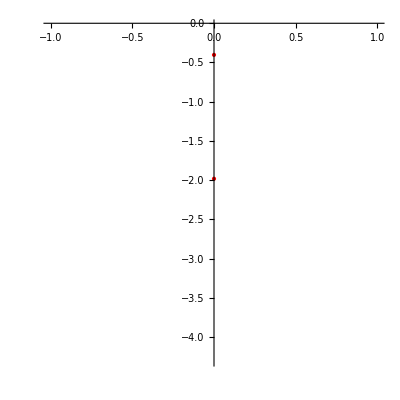
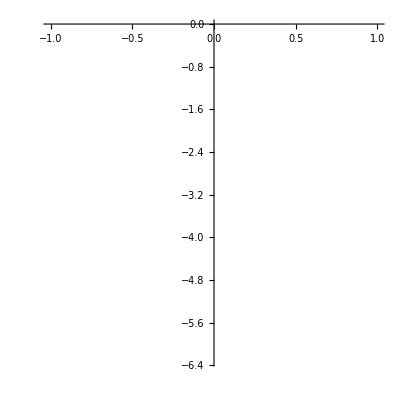
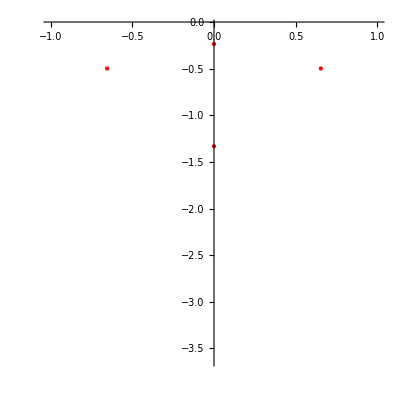
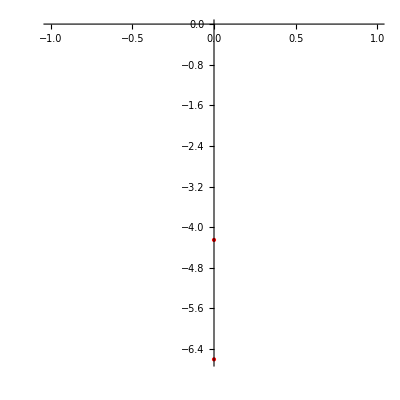
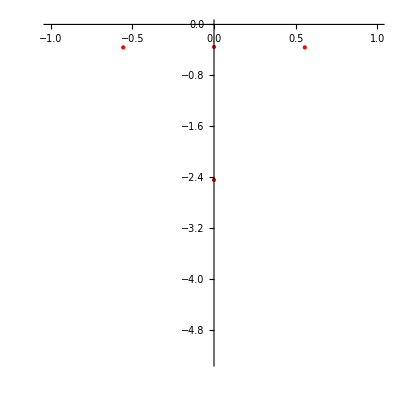

```mathematica
Function[i,Graphics[{Red,PointSize[Large],Point[{Re[#],Im[#]}&/@Eigenvalues[Hlist[[i]]]]},Axes->True,AspectRatio->1,AxesOrigin->{0,0},PlotRange->{{-1,1},All}]]/@Range[61,80]
```

```mathematica
eiglist//Dimensions
```

{100,300}

```mathematica
gamma=Select[#//Chop,I*Im[#]==#&]&/@eiglist;
```

```mathematica
gammas=Sort/@Im/@(gamma/.{}->Sequence[]);
```

```mathematica
imlist=Flatten@Position[gamma,_?(#≠{}&)];
```

```mathematica
cond=ParallelTable[Chop@G[x,hwlist[[i,1]],W1],{i,imlist},{x,-.05,.05,.001}];
```

```mathematica
condmean=Mean/@cond;
```

```mathematica
gc=MapThread[Append[#1,#2]&,{gammas,condmean}];
```

```mathematica
gammaratio=gammas[[All,1]]/gammas[[All,2]];
```

```mathematica
grc=Transpose@{Log@gammaratio,condmean};
```

```mathematica
1/gammas[[All,1]]
```

{-6.08186,-5.85028,-57.3493,-23.1621,-5.62662,-27.4243,-3.66774,-35.3968,-30.7978,-8.85818,-8.80782,-14.8499,-3.66635,-24.4931,-4.55818,-23.1764,-10.2575,-8.18371,-21.6852,-12.4823,-19.0904,-16.1707,-23.6984,-21.0813,-15.9562,-4.18068,-30.2521,-7.85549,-9.52593,-21.6667,-9.83974,-13.1934,-8.54159,-10.9291,-27.0295,-15.6586,-4.13434,-15.4322,-12.3335,-26.5417,-8.50007,-6.74078,-9.46753,-4.35084,-31.9633,-85.2623,-23.6146,-9.62205,-9.80913,-12.3966,-49.8457,-5.86664,-9.97375,-5.23342,-38.7236,-26.609,-9.98062,-5.92776,-10.8953,-16.3196,-51.9974,-14.526,-13.0934,-4.74713,-13.1475,-10.6965,-13.1915,-13.3577,-33.0283,-4.74104,-19.9238,-6.96473,-11.8513,-13.6559,-25.1573,-22.3979,-7.2519,-26.1932,-16.6439,-9.12851,-11.1317,-10.8166,-8.28717,-67.3188,-12.0129,-35.3194,-11.1737,-8.1604,-23.1394,-26.1576,-8.64235,-28.9597,-13.2496,-7.83546,-26.3576,-57.5066,-9.01269,-7.16985,-7.08862,-5.73103,-16.3269,-18.7406,-10.3231,-7.94289,-11.6013,-11.9843,-14.7664,-5.5777,-12.2389,-5.24636,-16.8026,-7.78437,-21.0746,-11.8543,-9.53314,-33.1024,-10.2128,-18.8301,-15.3524,-4.40749,-15.8731,-13.2798,-4.65217,-15.0864,-9.55277,-11.4213,-7.05407,-6.87224,-11.7496,-9.42528,-30.2539,-42.6553,-82.3008,-7.6068,-7.7727,-9.04889,-19.8013,-30.2149,-14.7772,-4.75238,-31.8988,-14.3908,-18.992,-8.49258,-13.1406,-17.8787,-11.0641,-8.4872,-33.7016,-7.50432,-19.7515,-6.05579,-4.76139,-8.4014,-32.9012,-19.6383,-11.0508,-8.99092,-7.6541,-9.22007,-32.6338,-13.2635,-34.6047,-3.3459,-7.59334,-5.42038,-5.43039,-34.255,-13.8272,-6.03793,-54.8913,-6.56368,-15.4029,-17.2947,-16.768,-11.7627,-10.0802,-39.7614,-13.9597,-10.0808,-8.23338,-4.88928,-11.5743,-12.1086,-5.5516,-14.7393,-26.9339,-11.4419,-9.66559,-15.435,-9.48153,-7.62392,-4.69444,-15.4304,-9.43986,-29.3774,-14.4213,-13.1328,-17.8696,-22.5228,-23.6295,-15.5532,-6.79092,-14.2414,-7.26957,-13.9011,-47.8354,-43.9721,-8.31036,-9.65653,-11.0421,-10.0041,-15.5487,-8.66383,-31.0709,-22.9525,-24.6805,-21.1313,-16.6994,-11.6084,-6.10131,-8.48201,-43.0283,-13.8254,-10.513,-6.53596,-19.1268,-9.01188,-27.3194,-16.2605,-21.239,-9.48776,-20.4602,-24.7454,-21.7085,-14.3212,-9.23715,-9.86094,-9.09093,-19.1064,-45.9119,-18.1729,-14.1632,-12.4721,-26.677,-7.46504,-7.07369,-10.9916,-14.7453,-7.83812,-11.2084,-37.7175,-13.3042,-3.97073,-8.31051,-40.0253,-7.83083,-12.3103,-7.54857,-11.1048,-4.9186,-6.98048,-12.3184,-14.8487,-12.7328,-50.6768,-17.1459,-8.66467,-18.2385,-19.5475,-10.3932,-8.11417,-26.9074,-16.4172,-169.159,-7.96669,-15.5472,-17.0099,-9.52001,-5.82437,-4.45806,-35.5204,-28.3202,-6.22317,-10.3552,-21.2348,-24.9472,-17.5409,-9.65366,-6.70237,-10.1144,-5.23725,-12.6208,-5.33487,-10.2217,-7.16924,-32.7974,-13.7681,-15.5867,-104.172,-9.73348,-19.0828,-11.7402,-6.99411,-28.386,-21.0114,-22.7724,-24.2935,-21.8577,-23.7144,-6.73203,-9.71825,-40.538,-3.38277,-12.1839,-14.8354,-9.20695,-12.3595,-5.53312,-9.78607,-12.9387,-15.8796,-7.1182,-13.2031,-6.74195,-21.2025,-12.5413,-9.56614,-6.30706,-10.182,-43.2699,-10.3283,-13.0465,-12.0092,-9.66684,-10.079,-16.3828,-4.27862,-3.04155,-12.5404,-13.6714,-7.16836,-10.0029,-16.3857,-13.1664,-6.41828,-37.141,-44.0849,-9.34995,-6.04491,-9.71106,-36.5846,-13.7186,-25.7749,-7.48375,-12.3463,-27.2639,-14.9855,-31.0643,-9.28859,-15.6605,-6.56677,-18.7118,-13.3642,-7.32616,-10.1084,-7.85219,-4.19823,-17.9878,-6.66856,-9.80646,-230.399,-20.1376,-15.6527,-14.2056,-16.5972,-8.59635,-16.0589,-32.0193,-8.78011,-21.1095,-15.5169,-7.21434,-20.2226,-13.287,-10.5998,-9.51235,-22.1414,-6.15912,-5.66127,-29.3436,-5.63152,-13.1488,-4.11134,-6.25862,-11.2056,-15.2942,-7.74916,-13.9774,-31.9405,-15.859,-7.29696,-12.1193,-22.6588,-11.1484,-9.9989,-30.9808,-7.33431,-16.4789,-9.35627,-19.0598,-6.09493,-12.2542,-7.38993,-24.5457,-11.265,-6.83675,-3.13188,-8.23369,-8.2308,-9.4904,-25.528,-11.0819,-31.4674,-12.489,-25.8495,-11.1462,-18.618,-58.2924,-7.17596,-6.23148,-7.5684,-13.4996,-5.95967,-17.7428,-16.1042,-7.78362,-11.2427,-5.31247,-9.20809,-4.52107,-20.7519,-9.64566,-12.6523,-25.0929,-10.4499,-15.8374,-8.74772,-15.6463,-7.54458,-57.3223,-15.5258,-7.87343,-16.3586,-21.5681,-4.99353,-30.7224,-11.8176,-8.88663,-16.1505,-10.0491,-10.3534,-7.39128,-9.40628,-30.3435,-10.5509,-35.2272,-70.1636,-38.2313,-6.60847,-17.1426,-6.67385,-14.0343,-27.8504,-20.0792,-11.0671,-9.208,-6.49724,-11.5957,-13.1155,-13.1416,-16.4746,-5.88233,-20.8781,-17.1361,-22.115,-5.54241,-12.3351,-37.6149,-8.0688,-4.32627,-5.98526,-7.70581,-10.6476,-9.90551,-15.1729,-29.5258,-7.49471,-27.4549,-9.11285,-37.9389,-18.3076,-28.9269,-28.9397,-22.436,-7.31247,-22.3027,-21.1921,-15.3333,-9.97609,-15.8517,-33.1597,-16.7179,-8.91743,-34.9005,-20.2423,-17.8767,-37.149,-7.33446,-9.36488,-18.3477,-47.7135,-7.07357,-13.9186,-15.2656,-13.154,-4.86374,-25.0939,-17.4165,-9.97215,-16.0089,-12.8296,-12.9941,-11.1342,-7.10329,-7.67679,-44.4363,-13.4069,-6.11714,-8.67815,-14.6942,-6.39464,-28.9302,-3.54971,-8.71186,-11.849,-21.0056,-14.4264,-12.1972,-8.8074,-8.88984,-22.2769,-9.44068,-9.94331,-30.8633,-10.7119,-8.75818,-16.6083,-29.87,-48.9912,-10.9255,-9.67043,-7.08873,-40.1423,-12.8348,-7.608,-24.7996,-27.6449,-18.4873,-16.8774,-15.845,-6.38763,-9.99421,-7.78964,-12.7248,-13.2204,-31.5773,-8.09144,-13.1372,-19.5021,-11.2264,-8.63046,-13.8772,-29.3947,-19.2214,-58.4228,-14.5893,-19.6004,-7.55919,-9.85499,-22.4321,-13.5839,-16.0202,-15.7126,-11.39,-18.1413,-14.4322,-7.82147,-6.75022,-14.7491,-29.0153,-11.2825,-9.43797,-42.092,-18.7377,-13.4338,-8.3381,-11.3838,-10.9078,-14.6418,-10.27,-17.6237,-20.8769,-12.011,-10.7645,-8.75357,-9.08897,-16.7294,-10.608,-11.3133,-25.9429,-9.37572,-7.80401,-4.82464,-11.6631,-16.2103,-37.2531,-10.8189,-23.3815,-11.2591,-16.8134,-13.6734,-9.90823,-5.55241,-27.4272,-8.23145,-11.6729,-18.308,-8.29762,-12.3481,-29.397,-11.1313,-8.95387,-28.4011,-12.791,-10.4008,-8.65372,-13.2053,-7.29316,-7.55513,-14.5148,-9.06525,-11.4818,-11.9533,-12.099,-4.16867,-14.004,-6.06347,-9.50434,-23.6466,-12.9894,-18.2368,-29.7002,-18.9368,-10.5834,-10.483,-21.981,-12.7959,-68.4335,-17.1212,-4.37441,-20.7122,-25.3628,-25.5487,-8.31868,-10.6206,-15.2108,-22.3634,-42.0465,-61.5577,-11.7403,-34.592,-7.68911,-7.28905,-29.8064,-10.1427,-14.3391,-29.3794,-5.84889,-18.6706,-9.93809,-23.7486,-20.2248,-28.3716,-11.2265,-4.08229,-16.6265,-8.33536,-13.1003,-30.5662,-7.26606,-11.5532,-13.1828,-37.4903,-9.62401,-10.5457,-3.65416,-31.2963,-11.6251,-5.82612,-12.0939,-13.5033,-9.0461,-12.9805,-16.3465,-21.8947,-12.2457,-7.47641,-11.6682,-8.78999,-14.1887,-16.9727,-6.6545,-10.4933,-21.3212,-10.9895,-6.91016,-33.4222,-9.20167,-5.16884,-40.7074,-16.9897,-8.09591,-39.863,-5.51004,-4.02736,-6.68949,-12.9265,-5.64947,-15.0427,-24.7373,-7.54465,-4.64193,-18.3189,-9.84154,-12.302,-11.6327,-5.0057,-43.3968,-16.3771,-18.8179,-17.8447,-27.4903,-15.8565,-11.8366,-19.722,-8.04786,-12.0983,-4.40355,-8.86669,-4.77218,-7.41437,-15.2217,-12.7629,-5.82074,-6.55484,-14.2963,-7.40758}

```mathematica
cgr=Transpose@{condmean,Log[-1/gammas[[All,2]]+1/gammas[[All,1]]]};
```

```mathematica
imlist
```

{1,2,6,7,8,10,11,12,15,17,18,21,22,24,26,27,28,29,30,31,32,33,34,36,37,38,41,42,44,45,47,48,49,51,53,54,55,56,57,59,61,62,63,64,66,67,68,69,72,74,75,77,78,80,82,84,85,86,89,91,95,98,99}

```mathematica
gammas
```

{{-0.0600785,-0.00228565},{-0.0298197,-0.0109185},{-0.0649897,-0.0140245},{-0.050212,-0.0191975}}

```mathematica
condmean
```

{1.57444,1.1733,0.748884,0.859248}

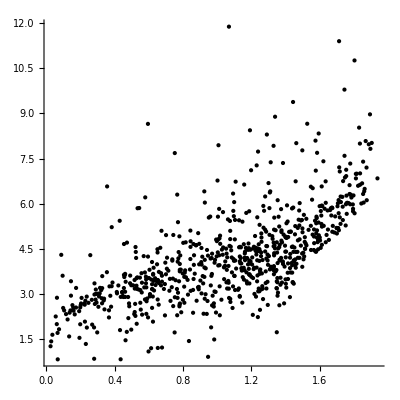

```mathematica
Graphics[Point@cgr,PlotRange->All,AspectRatio->1,Axes->True,AxesOrigin->{0,0},FrameLabel->{"G","E"}]
```

```mathematica
Position[Log@gammaratio,_?(8.1<#&)]
```

{{204},{260},{313}}

```mathematica
Log@gammaratio[[313]]
```

8.17149

```mathematica
gammas[[313]]
```

{-0.0246682,-6.97117×10^-6}

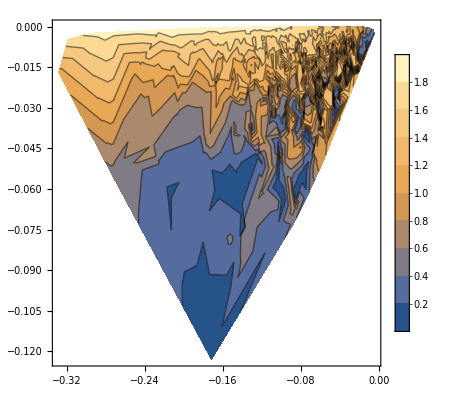

```mathematica
ListContourPlot[gc,PlotRange->Full,PlotLegends->Automatic]
```

```mathematica
{H1,W1}=hwlist[[1]];
```

```mathematica
{H2,W2}=hwlist[[24]];
```

```mathematica
enlist=ParallelTable[G[x,H1,W1]//Chop,{x,-1,1,0.01}];//AbsoluteTiming
```

{0.0593317,Null}

```mathematica
enlist2=ParallelTable[G[x,H2,W2]//Chop,{x,-2,2,0.01}];//AbsoluteTiming
```

{0.0781428,Null}

```mathematica
enlist3=ParallelTable[Gr[x,H1,W1]//Chop,{x,-2,2,0.01}];//AbsoluteTiming
```

{0.0830264,Null}

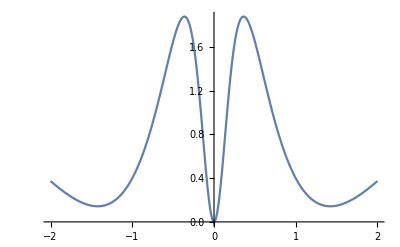

```mathematica
ListLinePlot[enlist,PlotRange->All,DataRange->{-2,2}]
```

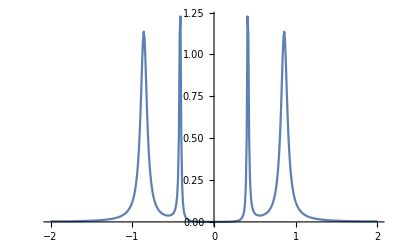

```mathematica
ListLinePlot[enlist2,PlotRange->All,DataRange->{-2,2}]
```

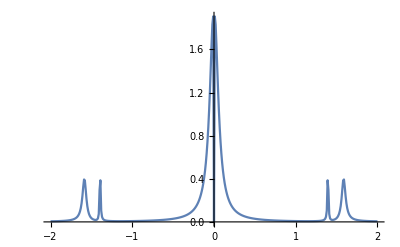

```mathematica
ListLinePlot[enlist3,PlotRange->All,DataRange->{-2,2}]
```

```mathematica
enmap=ParallelTable[G[x,(1-α)*H1+(α)*H2,W1],{x,-1,1,0.01},{α,0,1,0.01}];//AbsoluteTiming
```

{1.69974,Null}

```mathematica
enmap3=ParallelTable[Gr[x,(1-α)*H1+(α)*H2,W1],{x,-1,1,0.01},{α,0,1,0.01}];//AbsoluteTiming
```

{11.0275,Null}

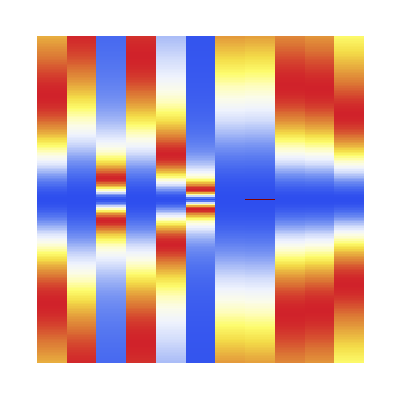

```mathematica
ArrayPlot[enmap,AspectRatio->1,ColorFunction->"TemperatureMap"]
```

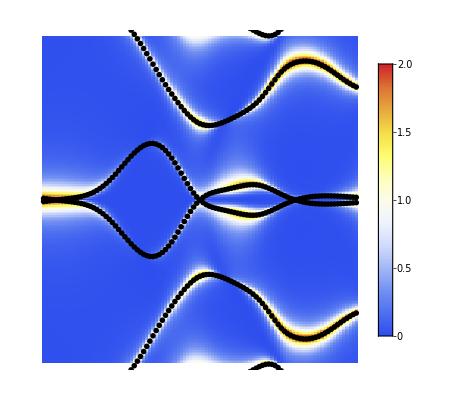

```mathematica
ArrayPlot[Re@enmap,ColorFunction->"TemperatureMap",DataRange->{{0,1},{-1,1}},PlotLegends->Automatic,PlotRange->Full,AspectRatio->1,FrameTicks->True,Epilog->{ First@eigplot}]
```

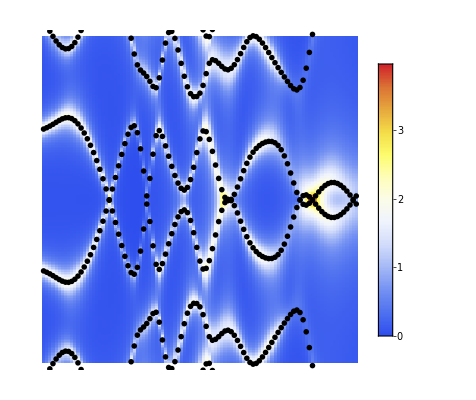

```mathematica
ArrayPlot[Re@enmap3,ColorFunction->"TemperatureMap",DataRange->{{0,1},{-1,1}},PlotLegends->Automatic,PlotRange->Full,AspectRatio->1,FrameTicks->True,Epilog->{ First@eigplot}]
```

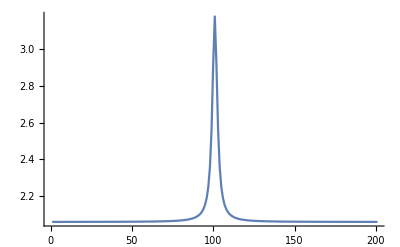

```mathematica
ListPlot[enmap[[All,1]],PlotRange->Full,Joined->True]
```

```mathematica
eiglist=ParallelTable[Eigenvalues[(1-α)*H1+(α)*H2],{α,0,1,0.01}];
```

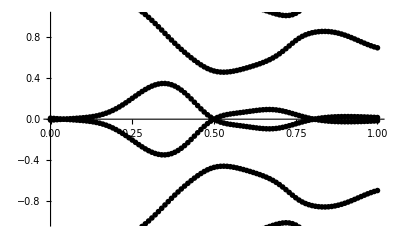

```mathematica
eigplot=ListPlot[Transpose@eiglist,DataRange->{0,1},PlotRange->{All,{-1,1}},PlotStyle->Directive[PointSize[.01],Black]]
```

```mathematica
x1=RandomVariate[NormalDistribution[],10000];
```

```mathematica
x2=RandomVariate[NormalDistribution[],10000];
```

```mathematica
smd1=(First@SmoothHistogram[x1])[[2,1,3,3,1]];
```

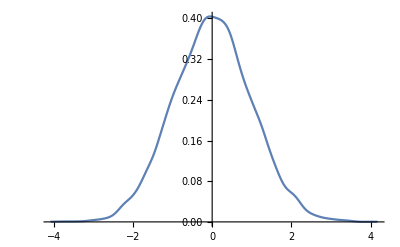

```mathematica
SmoothHistogram[x1]
```

```mathematica
smd2=(First@SmoothHistogram[x2])[[2,1,3,3,1]];
```

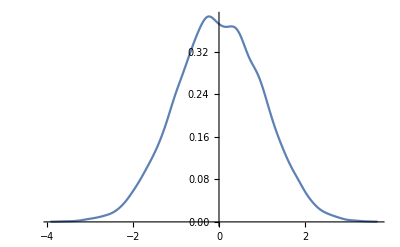

```mathematica
SmoothHistogram[x2]
```

```mathematica
smd3=(First@SmoothHistogram[(x1-x2)/√2])[[2,1,3,3,1]];
```

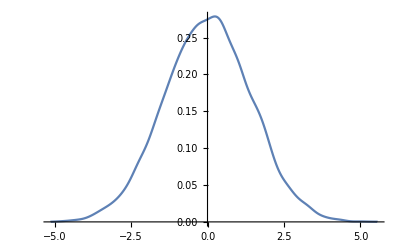

```mathematica
SmoothHistogram[x1-x2]
```

```mathematica
FindFit[smd1,a*Exp[-x^2/(2 b^2)],{a,b},x]
```

{a→0.400163,b→0.995801}

```mathematica
FindFit[smd2,a*Exp[-x^2/(2 b^2)],{a,b},x]
```

{a→0.389227,b→1.02993}

```mathematica
FindFit[smd3,a*Exp[-x^2/(2 b^2)],{a,b},x]
```

{a→0.393453,b→1.01524}

```mathematica
gn=Range[0.1,1,0.1]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
prob={2691/100000,27560/500000,854/10000,1177/10000,1641/10000,2188/10000,2809/10000,3544/10000,4782/10000,376181/500000}//N
```

{0.02691,0.05512,0.0854,0.1177,0.1641,0.2188,0.2809,0.3544,0.4782,0.752362}

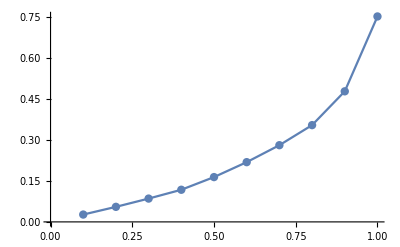

```mathematica
ListLinePlot[prob,DataRange->{.1,1},Mesh->All]
```

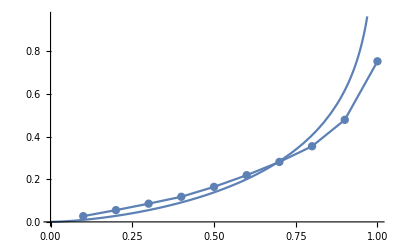

```mathematica
Plot[-√(2 x/(8π))Log[1-x],{x,0,1},Epilog->{First@ListLinePlot[prob,DataRange->{.1,1},Mesh->All]}]
```

```mathematica
Limit[-√(2 x/(8π))Log[1-x],{x->1}]
```

∞

```mathematica
-√(2 x/(8π))Log[1-x]/.x->0.99
```

1.29258

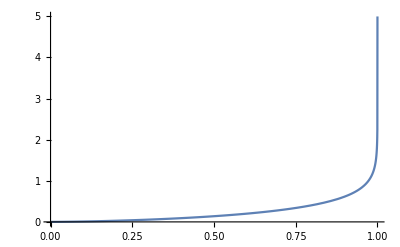

```mathematica
Plot[-√(2 x/(8π))Log[1-x],{x,0,1},PlotRange->Full]
```